```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/kempsilonnaught/Builds/CellSurfaceFE/MongeParameterization/SimpleTwoInclusionLift

```mathematica
FileNames[]
```

{cell_forces350.000000.gpl,cell_forces.dx,cell_forces.eps,cell_forces.gpl,cell_forces.svg,CMakeCache.txt,CMakeFiles,cmake_install.cmake,CMakeLists.txt,first_stab_at_two_inclusion_lift,first_stab_at_two_inclusion_lift.jpeg,laplacian_two_inclusion,main.cpp,Makefile,Makefile.old_and_busted,second_stab_actually_works.jpeg,second_stab_actually_works.png,testexe,testexe2,testgrid.eps,TwoInclusionLift_assemble.cpp,TwoInclusionLift_cell_mesh.cpp,TwoInclusionLift.h,twoinclusionlift_output.cpp,TwoInclusionLift_run.cpp,TwoInclusionLift_setup.cpp,TwoInclusionLift_solve.cpp,Visualization_Time.nb}

```mathematica
?ReadList
```

ReadList[file] reads all the remaining expressions in a file and returns a list of them. 
ReadList[file,type] reads objects of the specified type from a file, until the end of the file is reached. The list of objects read is returned. 
ReadList[file,{type_1,type_2,…}] reads objects with a sequence of types, until the end of the file is reached. 
ReadList[file,types,n] reads only the first n objects of the specified types.

```mathematica
stream = OpenRead["cell_forces.gpl"];
```

```mathematica
Skip[stream,Record,7]
```

```mathematica
data=ReadList[stream,{Number,Number,Number}];
```

```mathematica
Close[stream]
```

cell_forces.gpl

```mathematica
?BoxRatios
```

BoxRatios is an option for Graphics3D that gives the ratios of side lengths for the bounding box of the three-dimensional picture.

```mathematica
ListPlot3D[data,BoxRatios->Automatic]
```

-Graphics3D-

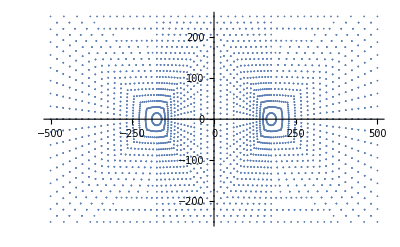

```mathematica
ListPlot[Transpose[Drop[Transpose[data],-1]]]
```